```mathematica
Needs["QMB`"]
```

SetDelayed::write: Tag Commutator in Commutator[A_,B_] is Protected.

```mathematica
d=3000;
ratiosData=Table[
evals=Eigenvalues[RandomVariate[GaussianOrthogonalMatrixDistribution[d]]];
Mean[SpacingRatios[evals,#]]&/@Range[20]
,100];
```

```mathematica
{Mean[#],StandardDeviation[#]}&[ratiosData]
```

{1.17577,0.00608704}

```mathematica
{Mean[#],StandardDeviation[#]}&[ratiosData]
```

{1.17674,0.00807944}

```mathematica
{Mean[#],StandardDeviation[#]}&[ratiosData]
```

{1.17782,0.00794877}

```mathematica
points={Mean[#],StandardDeviation[#]}&/@Transpose[ratiosData]
```

{{1.76745,0.0884952},{1.17696,0.00816355},{1.08547,0.00345619},{1.05199,0.00219573},{1.03531,0.00171281},{1.02591,0.00131399},{1.01991,0.00105626},{1.01593,0.000836213},{1.0131,0.000715448},{1.01103,0.000638646},{1.00947,0.000558463},{1.00824,0.0005117},{1.00731,0.000469941},{1.00653,0.000442795},{1.00591,0.000424786},{1.00539,0.00040427},{1.00495,0.000392007},{1.00459,0.000378266},{1.0043,0.000370519},{1.00405,0.000357685}}

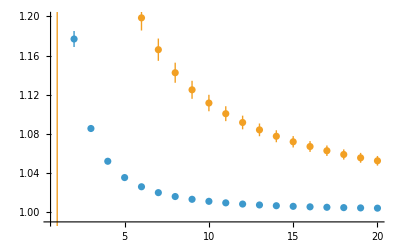

```mathematica
ListPlot[{
Transpose[{Range[20],Around@@@points}],
Transpose[{Range[20],Around@@@p}]
}
,PlotRange->{All,{0.99,1.20}}]
```

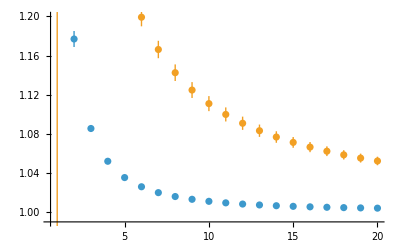

```mathematica
ListPlot[{
Transpose[{Range[20],Around@@@points}],
Transpose[{Range[20],Around@@@p}]
}
,PlotRange->{All,{0.99,1.20}}]
```

```mathematica
ratios=SpacingRatios[evals,2];
```

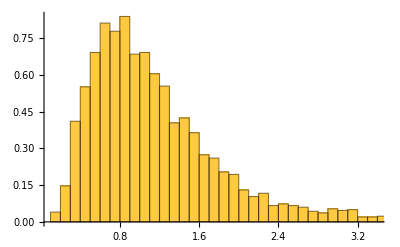

```mathematica
Histogram[ratios,"FreedmanDiaconis","PDF"]
```

```mathematica
Sqrt[Mean[#^2]-Mean[#]^2&[ratios]]
```

0.759391

```mathematica
StandardDeviation[ratios]
```

0.759518

```mathematica
evals=RandomReal[{-10,10},2000];
```

```mathematica
ratios=SpacingRatios[evals,1];
```

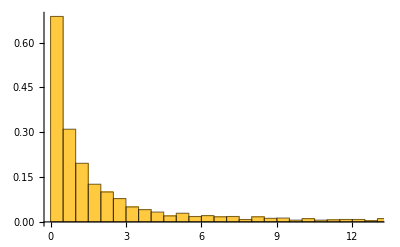

```mathematica
Histogram[ratios,"FreedmanDiaconis","PDF"]
```

```mathematica
Sqrt[Mean[#^2]-Mean[#]^2&[ratios]]
```

128.545

```mathematica
StandardDeviation[ratios]
```

128.577

```mathematica
Integrate[RatiosDistribution[r,1],{r,0,Infinity}]
Integrate[r*RatiosDistribution[r,1],{r,0,Infinity}]
Integrate[r^2*RatiosDistribution[r,1],{r,0,Infinity}]
```

1

7/4

Integrate::idiv: Integral of (27 r^3)/(8 (1+r+r^2)^(5/2))+(27 r^4)/(8 (1+r+r^2)^(5/2)) does not converge on {0,∞}.

∫_0^∞ (27 r^2 (r+r^2))/(8 (1+r+r^2)^(5/2))ⅆr

```mathematica
ratiosDataPoisson=Table[
evals=RandomReal[{-10,10},5000];
Mean[SpacingRatios[evals,#]]&/@Range[20]
,100];
```

```mathematica
p={Mean[#],StandardDeviation[#]}&/@Transpose[ratiosDataPoisson]
```

{{13.7208,24.2053},{1.99798,0.0725115},{1.49658,0.0229377},{1.33012,0.0141815},{1.24831,0.0104901},{1.19923,0.00931195},{1.16622,0.0088989},{1.14251,0.00847589},{1.12477,0.00810304},{1.11091,0.0076792},{1.09984,0.00717692},{1.09083,0.00677007},{1.08321,0.00629588},{1.07675,0.00587927},{1.07126,0.00549916},{1.06647,0.00519146},{1.06226,0.00496555},{1.05853,0.00475161},{1.05522,0.00455932},{1.05227,0.0043672}}